{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

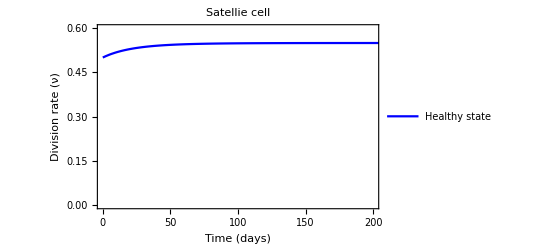

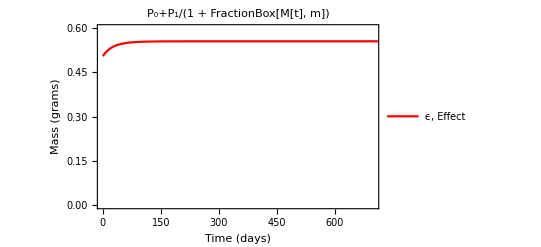

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;m=1000;d=0.05;
s=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==250.31,M[0]==4755.9},{S,M},{x,0,900}]
g=Plot[Evaluate[(*v0+v1/(1+{{M[x]}/.s}/m)*){0.002*{S[x]}/.s}],{x,0,900},PlotRange->{{0,200},{0,0.6}},PlotStyle->Blue,(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)PlotLegends->{"Healthy state"},AxesStyle->Directive[Black,12],GridLines->{{443},{}},Frame->True,FrameLabel->{"Time (days)","Division  rate (ν)"},FrameStyle->Directive[Black,12],PlotLabel->"Satellie cell",LabelStyle->Directive[Bold,Black]]
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.49941;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.0;d2=0.0;
s1=NDSolve[{TT'[x]==(0.244597*TT[x])/((1+(TT[x]/1088.66)^μ)^(1/μ)),SS'[x]==(2 *(P0+P1/(1+MM[x]/m))-1)* (v0+v1/(1+MM[x]/m)-ϵ*TT[x]/(1+TT[x]/m2))*SS[x]-((d1*TT[x])/(1+(TT[x]/m2)))*SS[x],MM'[x]==2 *(1-P0-P1/(1+MM[x]/m))*(v0+v1/(1+MM[x]/m)-ϵ*TT[x]/(1+TT[x]/m2))* SS[x]-(d+((d2*TT[x])/(1+(TT[x]/m2))))*MM[x],TT[0]==6.86,SS[0]==252.5,MM[0]==4797.08},{TT,SS,MM},{x,0,900}];
g1=Plot[Evaluate[(*v0+v1/(1+{{M[x]}/.s1}/m)*)(*v0+v1/(1+{{MM[x]}/.s1}/m)-ϵ*{{T[x]}/.s1}/(1+{({T[x]}/.s1)/10})*){0.002*{SS[x]}/.s1}],{x,0,900},PlotRange->{{0,700},{0,0.6}},PlotStyle->Red(*,AxesLabel->{"Time (days)","P_0+P_1/(1+M[mm^3]/m)"}*),PlotLegends->{"ϵ, Effect"},AxesStyle->Directive[Black,12],AxesStyle->Directive[Black,12],(*GridLines->{{443},{}}*)Frame->True,FrameLabel->{"Time (days)","Mass (grams)"},FrameStyle->Directive[Black,12],PlotLabel->"P_0+P_1/(1 + FractionBox[M[t], m])",LabelStyle->Directive[Bold,Black]]
```

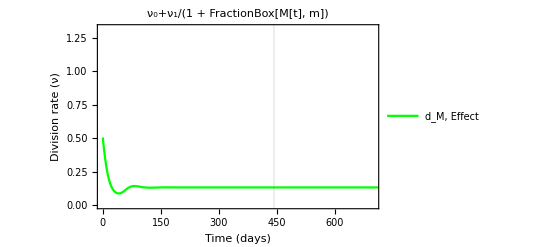

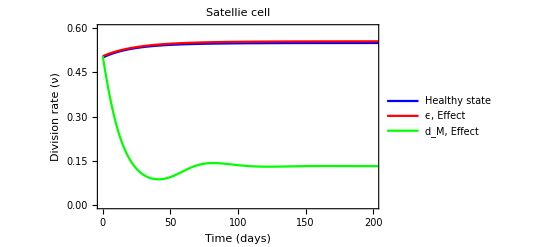

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.49941;m=1000;d=0.05;m2=1.001;ϵ=0.00;d1=0.07;d2=0.0;
s2=NDSolve[{TTT'[x]==(0.244597*TTT[x])/((1+(TTT[x]/1088.66)^μ)^(1/μ)),SSS'[x]==(2 *(P0+P1/(1+MMM[x]/m))-1)* (v0+v1/(1+MMM[x]/m)-ϵ*TTT[x]/(1+TTT[x]/m2))*SSS[x]-((d1*TTT[x])/(1+(TTT[x]/m2)))*SSS[x],MMM'[x]==2 *(1-P0-P1/(1+MMM[x]/m))*(v0+v1/(1+MMM[x]/m)-ϵ*TTT[x]/(1+TTT[x]/m2))* SSS[x]-(d+((d2*TTT[x])/(1+(TTT[x]/m2))))*MMM[x],TTT[0]==6.86,SSS[0]==252.5,MMM[0]==4797.08},{TTT,SSS,MMM},{x,0,900}];
g2=Plot[Evaluate[(*v0+v1/(1+{{MM[x]}/.s2}/m)*)(*v0+v1/(1+{{MM[x]}/.s2}/m)-ϵ*{{T[x]}/.s2}/(1+{({T[x]}/.s2)/10})*){0.002*{SSS[x]}/.s2}],{x,0,900},PlotRange->{{0,700},{0,1.32}},PlotStyle->Green(*,AxesLabel->{"Time (days)","P_0+P_1/(1+M[mm^3]/m)"}*),PlotLegends->{"d_M, Effect"},AxesStyle->Directive[Black,12],AxesStyle->Directive[Black,12],GridLines->{{443},{}},Frame->True,FrameLabel->{"Time (days)","Division rate (ν)"},FrameStyle->Directive[Black,12],PlotLabel->"ν_0+ν_1/(1 + FractionBox[M[t], m])",LabelStyle->Directive[Bold,Black]]
Show[g,g1,g2]
```